Options

Many functions in the Wolfram Language have options that determine the details of how they work. For example, in making a plot, you can use PlotTheme→"Web" to use a web-oriented visual theme. On a keyboard, the → is automatically formed if you type -> (i.e. - followed by >).

A standard plot, with no options given:

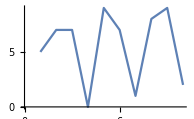

```mathematica
ListLinePlot[RandomInteger[10,10]]
```

A plot with the PlotTheme option given as "Web":

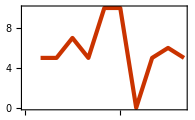

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web"]
```

A plot with the PlotTheme option given as "Detailed":

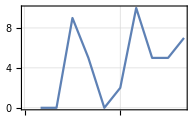

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Detailed"]
```

A plot with the PlotTheme option given as "Marketing":

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme-> "Marketing"]
```

-Graphics-

You can add more options. For example, Filling specifies what filling to add to a plot.

Fill the plot to the axis:

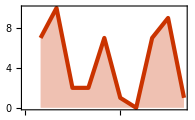

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis]
```

Background lets you specify a background color.

Also include an option for background color:

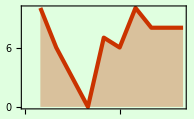

```mathematica
ListLinePlot[RandomInteger[10,10],PlotTheme->"Web",Filling->Axis,Background->LightGreen]
```

If you don’t mention a particular option, the Wolfram Language will use a pre-defined default for that option. Most often that default is Automatic, which means that the language will automatically determine what to do.

One option that’s often useful for graphics is PlotRange, which specifies what range of values to include in a plot. With the default PlotRange→Automatic, the system will try to automatically show the “interesting” part of the plot. PlotRange→All shows all values.

With default options all but one “outlier” value are displayed:

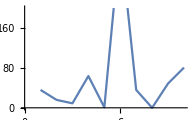

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81}]
```

PlotRange→All says to include all points:

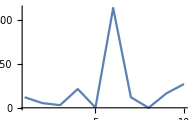

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->All]
```

PlotRange→30 specifies to show values up to 30:

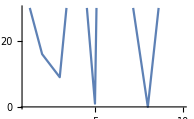

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->30]
```

PlotRange→{20,100} specifies to show values between 20 and 100:

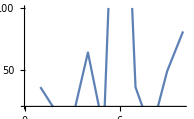

```mathematica
ListLinePlot[{36,16,9,64,1,340,36,0,49,81},PlotRange->{20,100}]
```

You can specify ranges for all types of graphics. In GeoListPlot and GeoGraphics you can use the option GeoRange to specify what part of the world to include in a plot.

By default, a geo plot of France pretty much includes only France:

```mathematica
GeoListPlot[LinguisticAssistant]
```

-Graphics-

This requests a range that includes all of Europe:

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant]
```

-Graphics-

GeoRange→All specifies to use the whole world:

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->All]
```

-Graphics-

There are many other options for GeoListPlot. For example GeoBackground specifies what kind of background should be used. GeoLabels adds labels. Joined makes the points be joined.

Use a relief map as the background:

```mathematica
GeoListPlot[LinguisticAssistant,GeoRange->LinguisticAssistant,GeoBackground->"ReliefMap"]
```

-Graphics-

Automatically add labels for geo objects:

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},GeoLabels->Automatic]
```

-Graphics-

Say it’s True that the points should be joined:

```mathematica
GeoListPlot[{LinguisticAssistant,LinguisticAssistant,LinguisticAssistant},Joined->True]
```

-Graphics-

The function ListLinePlot has 57 different options you can set; GeoListPlot has 54. Some options are common to all graphics functions. For example, AspectRatio determines the overall shape of graphics, specifying the ratio of height to width.

With an aspect ratio of 1/3, the plot is 3 times wider than it is tall:

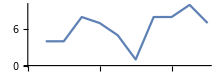

```mathematica
ListLinePlot[RandomInteger[10,10],AspectRatio->1/3]
```

The option ImageSize specifies the overall size of graphics.

Draw a circle with a “tiny” overall image size:

```mathematica
Graphics[Circle[ ],ImageSize->Tiny]
```

-Graphics-

Draw circles with specific image sizes between 5 and 50 pixels:

```mathematica
Table[Graphics[Circle[ ],ImageSize->n],{n,5,50,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

It’s not just Graphics that allows options. Lots of other functions do too. An example is Style, which supports many options.

Set an option to use "Chalkboard" font to style text:

```mathematica
Style["text in a different font",20,FontFamily-> "Chalkboard"]
```

text in a different font

It’s quite common for options to describe details of output, for example in WordCloud.

Create a word cloud with random word orientations:

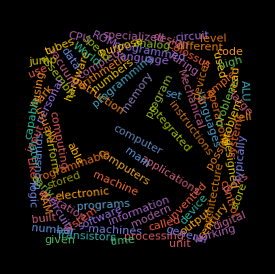

```mathematica
WordCloud[DeleteStopwords[WikipediaData["computer"]],WordOrientation->"Random"]
```

Grid has many options. The Frame option controls whether and how a frame is drawn.

Create a multiplication table with a frame around each entry:

```mathematica
Grid[Table[i*j,{i,5},{j,5}],Frame->All]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Like Graphics, Grid has a Background option:

```mathematica
Grid[Table[i*j,{i,5},{j,5}],Frame->All,Background->LightYellow]
```

1 | 2 | 3 | 4 | 5
2 | 4 | 6 | 8 | 10
3 | 6 | 9 | 12 | 15
4 | 8 | 12 | 16 | 20
5 | 10 | 15 | 20 | 25

Vocabulary

PlotTheme |   | theme for a plot (e.g. "Web", "Detailed", etc.) 
Filling |   | filling to add to a plot (Axis, Bottom, etc.) 
PlotRange |   | range of values to include in a plot (All, etc.) 
GeoRange |   | geo range to include (All, specific country, etc.) 
GeoBackground |   | background map ("ReliefMap", "OutlineMap", etc.) 
 GeoLabels |   | labels to add to a map (e.g. Automatic) 
Joined |   | whether to make points be joined (True, False)
Background |   | background color  
AspectRatio |   | ratio of height to width 
ImageSize |   | size in pixels 
Frame |   | whether to include a frame (True, All, etc.)
FontFamily |   | family of font to use (e.g. "Helvetica") 
WordOrientation |   | how to orient words in a word cloud

"13 Exercises Available"
"with 8 extras" | "Get Started »"

Create a list plot of Range[10] themed for the web. »

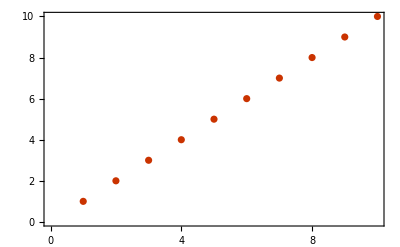
| Expected output: |  
  | -Graphics- |

Create a list plot of Range[10] with filling to the axis. »

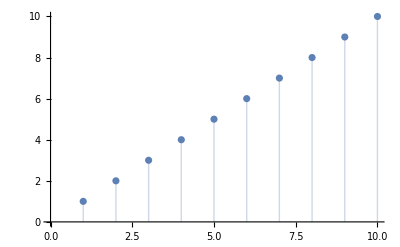
| Expected output: |  
  | -Graphics- |

Create a list plot of Range[10] with a yellow background. »

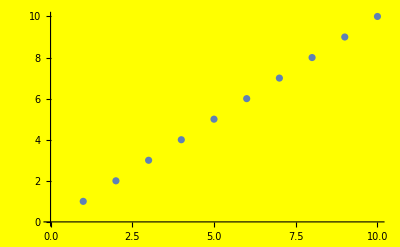
| Expected output: |  
  | -Graphics- |

Create a map of the world with Australia highlighted. »

| Expected output: |  
  | -Graphics- |

Create a map of the Indian Ocean with Madagascar highlighted. »

| Expected output: |  
  | -Graphics- |

Use GeoGraphics to create a map of South America showing topography (relief map). »

| Expected output: |  
  | -Graphics- |

Make a map of Europe with France, Finland and Greece highlighted and labeled. »

| Expected output: |  
  | -Graphics- |

Make a 12×12 multiplication table as a grid with white type on a black background. »

| Expected output: |  
  | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144 |

Make a list of 100 disks with random integer image sizes up to 40. »


| Sample expected output: |  
  | {,,,,,,,,,,,,,,,,,,,,,-Graphics-,,,,,,-Graphics-,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,-Graphics-,,-Graphics-,,,,,,,,,,-Graphics-,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,} |

Make a list of pictures of regular pentagons with image size 30 and aspect ratios from 1 to 10. »

| Expected output: |  
  | {,,,,,,,,,} |

Make a Manipulate that varies the size of a circle between 5 and 500. »

| Expected output: |  
  |  |

Create a framed 10×10 grid of random colors. »

| Sample expected output: |  
  | RGBColor[0.29206566845567505, 0.002125614288312816, 0.2466689715541872] | RGBColor[0.47138492775828, 0.4911528439664328, 0.31784307212771146] | RGBColor[0.7988533116473238, 0.4607738961445418, 0.932687977525182] | RGBColor[0.9921770810639374, 0.28669661704689964, 0.22611440899450508] | RGBColor[0.7853334751384575, 0.5106957592339412, 0.5932705334764325] | RGBColor[0.7940605090979496, 0.030832749065975884, 0.046642068859548136] | RGBColor[0.6639900419473621, 0.47730228595366286, 0.343633548056657] | RGBColor[0.6079723598484941, 0.9878962360284971, 0.29681614346009044] | RGBColor[0.9386808313819228, 0.4545617107616535, 0.08061283278295073] | RGBColor[0.8466678976391273, 0.43438692315766425, 0.45873078378244325]
RGBColor[0.42766178078008243, 0.8818108860362295, 0.002684852044487096] | RGBColor[0.698764636218167, 0.8841606315921906, 0.29643084398427977] | RGBColor[0.8277166560993325, 0.3986549234784509, 0.7272617341694452] | RGBColor[0.2640427892598227, 0.7301136860919337, 0.6496299716898004] | RGBColor[0.18313179810923375, 0.9241303062650972, 0.5658538596526743] | RGBColor[0.24991958553355342, 0.3568750293969678, 0.22586419653241352] | RGBColor[0.45947606947829134, 0.6824053817953912, 0.00024134211595638888] | RGBColor[0.6385867161016234, 0.570426867424229, 0.4284738245241415] | RGBColor[0.07368563860308974, 0.6966950301002717, 0.3576510244086333] | RGBColor[0.012857709609246593, 0.7355306943793138, 0.19598491635437343]
RGBColor[0.2835153513621751, 0.6604228786300981, 0.2200068210615027] | RGBColor[0.08883017948458138, 0.5741159561721454, 0.5311146208231401] | RGBColor[0.14213980318273922, 0.259663211745468, 0.7402643384761096] | RGBColor[0.06116978033592879, 0.7439905626421779, 0.020575546638970543] | RGBColor[0.7826961615706864, 0.6717407687528807, 0.7526999591352166] | RGBColor[0.48436818037075136, 0.8510409924212747, 0.26113864741688797] | RGBColor[0.37620783615983133, 0.09046485507099677, 0.7534186603663018] | RGBColor[0.82800276012107, 0.510081208124221, 0.38453910484830023] | RGBColor[0.48744555727863004, 0.45527488937800453, 0.5237969974746506] | RGBColor[0.739433425954608, 0.6785577447352407, 0.8609281256020811]
RGBColor[0.11198522728939553, 0.9086797696007514, 0.7250724541169944] | RGBColor[0.651473672432261, 0.43482286419454885, 0.3141586962094065] | RGBColor[0.7028679193119376, 0.4229359040071097, 0.08529571639115141] | RGBColor[0.1708513156268956, 0.5738601391991789, 0.4002071609592712] | RGBColor[0.1285903775261641, 0.23465011665489555, 0.0862700891468342] | RGBColor[0.36423293571388315, 0.17221066251426698, 0.5950835339743301] | RGBColor[0.35224197209298147, 0.059162760353133725, 0.059380609403944185] | RGBColor[0.27750309899168935, 0.09012266362751586, 0.5033043799419994] | RGBColor[0.4582322363185527, 0.6671610927845733, 0.6265425408879037] | RGBColor[0.7045704476218941, 0.9766982595838996, 0.5135537767686831]
RGBColor[0.7435615528713011, 0.8206778332951152, 0.1728719239287746] | RGBColor[0.2706201444036207, 0.5989776360880075, 0.05504043671795644] | RGBColor[0.5212143209731666, 0.13094329572290353, 0.4401702218046817] | RGBColor[0.4777142980485214, 0.6662249825946847, 0.7943824484061877] | RGBColor[0.4766645983618063, 0.4503518114975713, 0.2040237987104061] | RGBColor[0.8541378644384505, 0.7760453717740188, 0.8718006331155947] | RGBColor[0.6221595841189065, 0.2771791025719812, 0.2991604144197215] | RGBColor[0.738721911411738, 0.7864637997938844, 0.16429317695186052] | RGBColor[0.4341755215465799, 0.6754049581801993, 0.6093267149767296] | RGBColor[0.07397739131876158, 0.4434861026868726, 0.7073015509813647]
RGBColor[0.5449977349922017, 0.30689902275250036, 0.6431930946044215] | RGBColor[0.6802151220996493, 0.19780121348324697, 0.5784895230382427] | RGBColor[0.5761858379020335, 0.024134248378107293, 0.09005674858466461] | RGBColor[0.08980072565756525, 0.8924400235891128, 0.7027653332555279] | RGBColor[0.921013356115552, 0.5787843601810903, 0.8902205749541106] | RGBColor[0.14383223356933117, 0.20741245804295816, 0.43351294387694206] | RGBColor[0.9165845527003995, 0.9778359860262495, 0.019934723200675908] | RGBColor[0.8933498842191188, 0.6314813003798707, 0.4048720553975651] | RGBColor[0.9577257363542808, 0.5101851847586023, 0.21793811428702026] | RGBColor[0.32827900268599164, 0.18092667512053295, 0.18292101417654716]
RGBColor[0.9947234659842015, 0.7362673917528475, 0.17833543743798397] | RGBColor[0.9262681555407899, 0.12923865923775546, 0.8744616495907644] | RGBColor[0.1507106910015843, 0.7838368641846951, 0.12160676537795978] | RGBColor[0.022096964642620787, 0.05412201405012573, 0.20894427575148766] | RGBColor[0.1177574002937003, 0.8777391716133471, 0.9511067224886609] | RGBColor[0.9628667478752855, 0.5187148453672914, 0.48965318151031334] | RGBColor[0.9797906004603474, 0.37652813994899836, 0.912543314843036] | RGBColor[0.47767337706935087, 0.7803698229552118, 0.8513957703733555] | RGBColor[0.6186083855959468, 0.6172817181756793, 0.8362354274499046] | RGBColor[0.5686969106881692, 0.5706227822361789, 0.9397474496076712]
RGBColor[0.465486640887822, 0.012238098232026262, 0.5129620122777749] | RGBColor[0.7371388247813302, 0.7033136409163059, 0.34778506784928975] | RGBColor[0.17482105280546834, 0.9289246085099696, 0.9407716715672747] | RGBColor[0.963998470187061, 0.4989513378298567, 0.4346325431656395] | RGBColor[0.4922808170315851, 0.10142859193449771, 0.4387768202183584] | RGBColor[0.2932657403748373, 0.9592110666561684, 0.3370012402414748] | RGBColor[0.22531318483760887, 0.5120531909366199, 0.8412958283063041] | RGBColor[0.5554445044672778, 0.49975532501660647, 0.470290367389095] | RGBColor[0.19348149706391915, 0.5472637027818466, 0.18303505095952155] | RGBColor[0.1889888996860556, 0.9613650011425219, 0.9599966811229437]
RGBColor[0.032712433455355905, 0.09171477338105949, 0.6256526577060351] | RGBColor[0.037832888701319733, 0.6756110336396624, 0.4530739646366566] | RGBColor[0.12196366383064605, 0.7097758160285812, 0.2117448665310011] | RGBColor[0.0550119605253887, 0.9901979934074654, 0.9479059512747361] | RGBColor[0.2779218726182382, 0.74763105290484, 0.5742774676552009] | RGBColor[0.6297571164818849, 0.178662930383771, 0.5028200634717968] | RGBColor[0.8234508404983736, 0.2042763682300308, 0.7913752171263457] | RGBColor[0.8872550281420264, 0.3902425616258367, 0.8361662808771764] | RGBColor[0.8565935451911986, 0.49067845246225716, 0.17544615787959006] | RGBColor[0.8862070155335997, 0.7162460475914376, 0.3780672308711732]
RGBColor[0.036305674507441266, 0.3683226105337867, 0.35660343519284554] | RGBColor[0.760241264477344, 0.8228824737836888, 0.21973735308885378] | RGBColor[0.5967460028216434, 0.5183699749814739, 0.1465963532704213] | RGBColor[0.8071429971400006, 0.49168822495640674, 0.264291399559474] | RGBColor[0.40455978018176286, 0.37912541165142777, 0.3042791388820345] | RGBColor[0.5305129621262232, 0.45554651322742723, 0.8763444916443146] | RGBColor[0.13987852736249984, 0.79564523958578, 0.8232335980441428] | RGBColor[0.9487043467536898, 0.9522134148927992, 0.8526732618836614] | RGBColor[0.4675995947653995, 0.6227562411178003, 0.3418612371849121] | RGBColor[0.7875315370687437, 0.8866194848581064, 0.7558777597025088] |

Make a line plot of the lengths of Roman numerals up to 100, with a plot range that would be sufficient for all numerals up to 1000. »

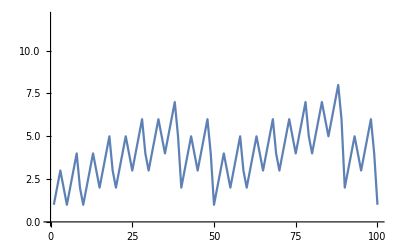
| Expected output: |  
  | -Graphics- |

Create a list plot of Range[10] with a frame included. »

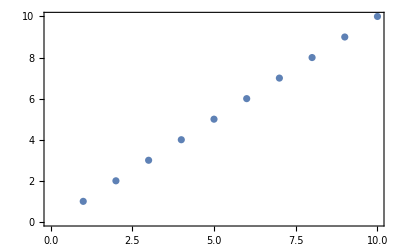
| Expected output: |  
  | -Graphics- |

Create a list plot of Range[10] with a yellow background and a frame. »

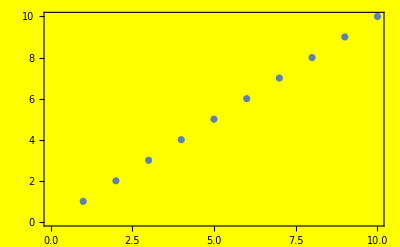
| Expected output: |  
  | -Graphics- |

Make a list of list plots of Range[10], with sizes ranging from 50 to 150 in steps of 10. »

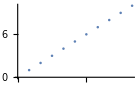
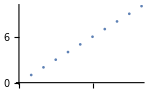
| Expected output: |  
  | {,,,,,,,,,-Graphics-,-Graphics-} |

Make a line plot of the first 20 squares, filling to the axis. »

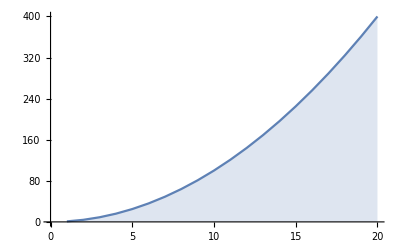
| Expected output: |  
  | -Graphics- |

Create a relief map of the region around Mount Everest, drawing a disk of radius 100 miles.  »

| Expected output: |  
  | -Graphics- |

Create a list plot of Range[10] with an aspect ratio of 1. »

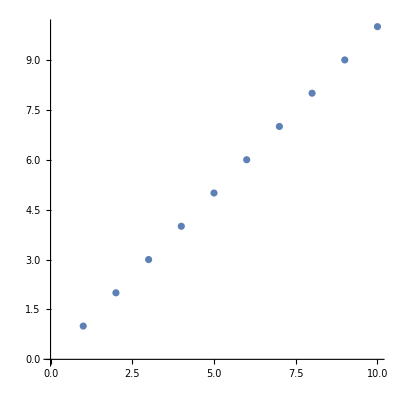
| Expected output: |  
  | -Graphics- |

Make a Manipulate that varies the aspect ratio of a picture of a regular hexagon from 0.1 to 5. »

| Expected output: |  
  |  |

Make a plot of the air temperature in Paris over the past week with the plot range restricted between 50 and 80 degrees. »

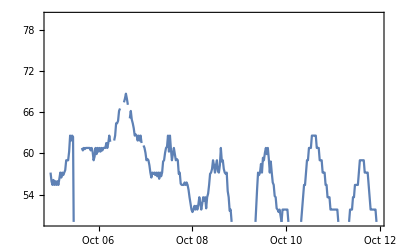
| Expected output: |  
  | -Graphics- |

Q&A

How can I get a list of the options for a function?

Look at the documentation. Or use for example Options[WordCloud]. Also, whenever you start typing the name of an option, you’ll see a menu of possible completions.

How do I find out the possible settings for an option?

Look at the documentation for that option. Also, when you type →, you’ll typically get a menu of possible common settings.

What is opt→value internally?

It’s Rule[opt,value]. Rules are used in lots of places in the Wolfram Language. a→b is usually read aloud as “a goes to b” or “a arrow b”.

When are values of options given as strings?

Only a small set of standard option settings (such as Automatic, None and All) are not strings. Specialized settings for particular options are normally strings.

Can one reset the default for an option?

Yes, using SetOptions. Though you have to be careful not to forget that you’ve done it.

Tech Notes

Many options can be set to be pure functions (see Section 26). It’s important to put parentheses in the correct place, as in ColorFunction→(Hue[#/4]&), or you won’t get the correct meaning.

$FontFamilies gives a list of possible settings for FontFamily.

More to Explore

Guide to Graphics Options in the Wolfram Language »

Guide to Formatting Options in the Wolfram Language »